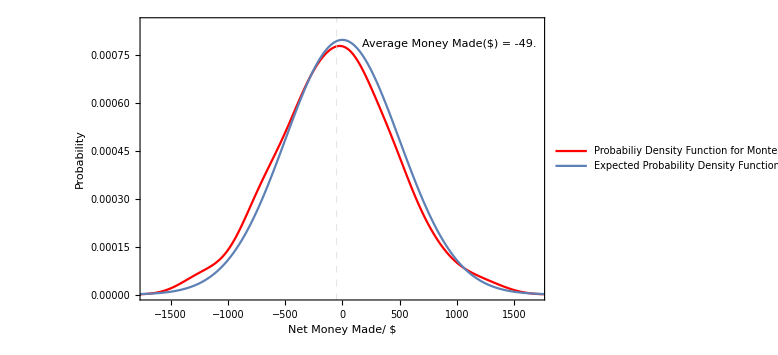

```mathematica
numberOfTrials = 0; 
probability = 1;
scorePerThrow = 50; (* this defines the number of levels we have*) 
results = List[];
iterator = 0; 
innerIter = 0; 
origBaseScore = 40000; 
lowerScore = 20000;
upperScore = 80000; 
targetScore = 42000; 
origLowerScore = lowerScore;
origUpperScore = upperScore; 
countInner = 100; 
countOuter = 100;
runningScore = origBaseScore; 

While [iterator < countOuter , 

While [ innerIter < countInner ,
			myRandom = RandomInteger[5];
			If [ myRandom == 0  ∨myRandom == 1 ∨ myRandom == 2 ,(* equal probability of increasing or decreasing score *) 
				runningScore = runningScore + scorePerThrow,
				runningScore  = runningScore - scorePerThrow
			   ];
	If[runningScore ≥  origUpperScore ∨  runningScore ≤  origLowerScore,
	runningScore = 0;
	Break[]
	];

	innerIter++;	
	];
If [ runningScore ≠ 0,
	AppendTo[results, (runningScore-origBaseScore)];
];
runningScore = origBaseScore;
innerIter = 0; 
iterator++; 
	];

results;

expectedData = List[]; 
iterator = 0;
endLocation = -1000;
number = 10000;
While [endLocation < 5000,
		endLocation = endLocation +scorePerThrow/10;
			
		probabilityValue = (number!)/(((number+endLocation)/2)!*((number-endLocation)/2)!)* ( 3/6)^((number+endLocation)/2)*( 3/6)^((number-endLocation)/2)/10;
		AppendTo[expectedData, {(endLocation*5),probabilityValue}];
		iterator++;
	]
expectedData;
p2 = ListPlot[expectedData, PlotRange->All, Joined -> True,LabelStyle->{FontSize->14, Directive[Bold,Black]}, Epilog->Inset[Framed[Grid[{{"Expected Average Money Made($) = "+Mean[expectedData] //N}},Alignment->{{Left}}],Background->Black],{0,0},{0,0}] ,PlotLegends-> {"Expected Probability Density Function \n Using Binomial Distribution"}];

dataHistogram = SmoothHistogram[results, GridLines-> { {Mean[results]}}, GridLinesStyle-> Dashed,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"Net Money Made/ $","Probability"(*,"Conditions= 
Starting Money = $40000; 
Money gained per each correct throw = $50;
FAIR dye i.e. P(WIN) = 3/6, P(LOSS) = 3/6
",""*)}, Epilog->Inset[Framed[Grid[{{"Average Money Made($) = "+Mean[results] //N}},Alignment->{{Left}}],Background->White],{1700,0.0008},{Right,Top}] ,  PlotLegends->{"Probabiliy Density Function \n for Monte-Carlo data"},LabelStyle->{FontSize->14, Directive[Bold,Black]}, PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}];
p2;
Show[{dataHistogram,p2} , PlotRange -> {{-1700,1700},{0,0.00085}}]
```